```mathematica
ClearAll[files, importfile, raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/1.2/1.2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/1.2/~$1.2.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/5 семестр (Квантовая физика)/1.2/1.2.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset1

```mathematica
dataset1 = makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"theta"->(#theta&),"n"-> (Around[#n, #dn] &)|>]
```

Dataset[<>]

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

```mathematica
line1 =LinearModelFit[(Normal@dataset1[All,{"theta","n"}/*Values]),{1,x},x]
```

FittedModel[1.31698+12.2157 x]

```mathematica
line1["ParameterTable"]
```

```mathematica
==
```

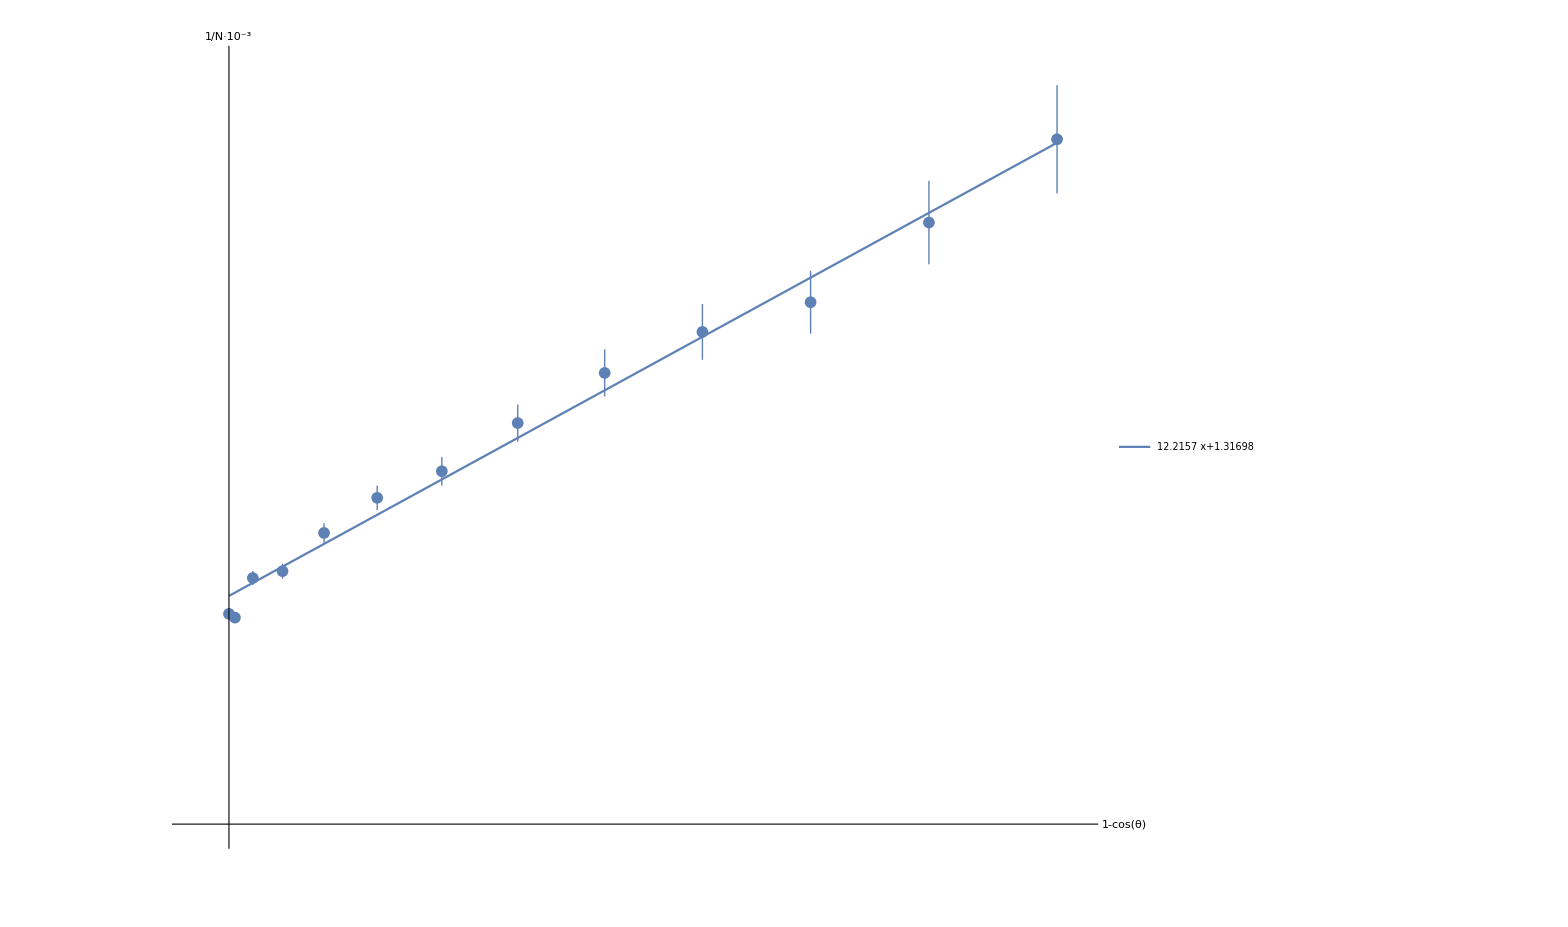

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
PlotRange-> {{-0.01,0.22},{-0.05, 4.4}},
Ticks-> {Range[-1000,1000, 0.05],Range[-1000,1000, 0.5]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["1-cos(θ)", Large], Style["1/N·10^-3", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.005],Range[-1000,1000, 0.1]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
Automatic,
{"V_2 = 4 В","V_2 = 6 В", "V_2 = 8 В"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.75]}
]
],
Plot[line1[x],{x,0,0.215},
PlotLegends->Placed[
LineLegend[
{Normal@line1},
LabelStyle->20,
LegendFunction->frame(*,
LegendLabel->"(dI/dU)_(u = 0)"*)
],
{Scaled[0.7],Scaled[0.3]}
]
]
]
```